# The Golden Ratio

## Introduction

The Golden Ratio is the irrational number τ = (1+√5)/2≃ 1.618 . Since antiquity, τ has attracted interests from mathematicians, physicists, philosophers, and artists.  Ancient Greeks believed that the golden rectangle, where the length to width ration is τ, provides the most pleasing proportion of all rectangles. Many of their architectural design include this shape as a result. Also, in arts, many painting contains rectangular shapes similar to the golden rectangle. But most applications of the Golden Ratio are in the natural sciences. This document explores the relationship between the Golden Ratio and the Fibonacci sequence.

## The Fibonacci sequence

The additive sequence is one of the best known numerical sequence. It originates from the relation A_(n+2)=A_(n+1)+A_n. For A_0=0 and A_1=1, it generates the Fibonacci sequence {F_n}_(n=1)^(n=∞). For example, the first ten elements of this sequence are 1,1,2,3,5,8,13,21,34,55 . In contrast, the geometric series is generated by the relation A_(n+1)=α A_n where α is a constant factor. 

When a sequence is both additive and geometric, the constant factor α must satisfy the second order equation α^2-α-1=0. It is usually called Fibonacci quadratic equation. The solutions of this equation are α = τ and α = -1/τ . In this example, the Golden Ratio is the specific value of the constant factor in the geometric sequence that makes the sequence additive.

The Golden Ratio satisfies the following limit τ=(n+1)/nn∞. The convergence of this limit is shown in Fig. 1.

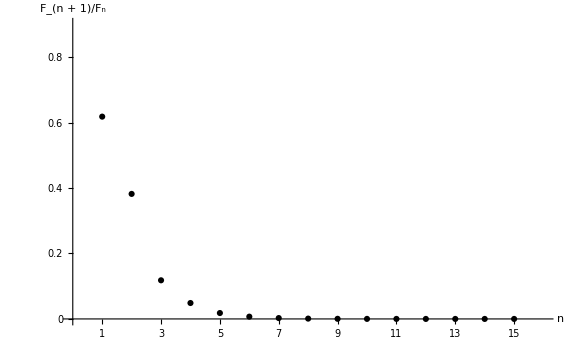
-Graphics-Fig. 1 The convergence the Fibonacci sequence to the Golden Ratio

```mathematica
Labeled[ListPlot[Abs[Fibonacci[Range[2,16]]/Fibonacci[Range[15]]-GoldenRatio],],Style["Fig. 1 The convergence the Fibonacci sequence to the Golden Ratio","Text",Larger]]
```

## The Fibonacci lattice

## Periodic arrays in 1D

The cut and projection method generates one dimensional (1D) periodic arrays. The basic principles of this method are as follows. Squares are used to generate a two-dimensional lattice. Then a cut line intersects the two-dimensional lattice. On the upper side of the line, the points nearest to the cut are projected onto the line. This procedure creates an array of segments on the cut. The periodicity of these segments is determined by the angle θ which the line makes with the edges of the squares. For different values of θ, the segments are shown in Fig. 2. For example, when tan(θ) equals a rational number, the sequence is periodic and the cut is called commensurate.

To construct periodic arrays in one dimension, I will define three functions. Let n^2 be the number of points in the two-dimensional lattice.

```mathematica
NearestPoints[n_,θ_]:=Map[Join[{#},NearestTo[Tan[θ]#][DeleteCases[Range[n], x_ /; x < Tan[θ]#]]]&,Range[n]]
```

This function selects the points nearest to the cut on the upper side only.

```mathematica
Projectors[poits_,θ_]:=Map[{Cos[θ],Sin[θ]}#&, Map[#.{Cos[θ],Sin[θ]}&,poits]]
```

Let “points” be a list of points. The above function projects the list of points on the cut.

```mathematica
PlotFnc[n_,θ_]:=Module[{points,proj},
points=NearestPoints[n,θ];
proj=Projectors[points,θ];
Labeled[
Plot[Tan[θ]x,{x,0,n+1},PlotRange->{{0,n+1},{0,n+1}},],Style["Fig. 2 The cut and projection method. The red points are the nearest points to the cut, which is the blue line.\n     The black points are the projections of the nearest points on the cut","Text",Larger]
]
]
```

Finally, this function plots the results of the cut and projection method for a given n and θ.

```mathematica
Manipulate[PlotFnc[n,θ],{{θ,ArcTan[1/GoldenRatio]},0,π/4},{{n,3},1,50,1},SaveDefinitions->True,LabelStyle->"DisplayFormula"]
```

When tan(θ)=τ^-1, the segments on the cut are the one dimensional Fibonacci sequence. This sequence is called one-dimensional Fibonacci lattice. This sequence cannot be generated by repeating a smaller portion of the sequence. But a fundamental property of the sequence is that τ^-1=n/(n+1)n∞. The Fibonacci lattice is then quasiperiodic and the cut is called incommensurate.

## Penrose tilings

Roger Penrose (1974) first studied two-dimensional Fibonacci lattices, which are called Penrose tilings. The construction of a Penrose tiling is similar to the cut and projection method described in the previous section. The Penrose tiling originates from an incommensurate cut and projections in a four-dimensional periodic (e.g. hypercubic) lattice. The tangent of the cut angle is related to the Golden Ratio. Figure 3 shows the Penrose tiling increasingly expanding in the x-y plane.

```mathematica
Manipulate[Module[{p={{-1,1,0,-1},{0,0,1,-1},{-1,1,0,0},{-1,0,1,-1}} (* Matrix form of Phi^-1 *),q (* Matrix form of Phi^-2 *),
rl={{0,0,0,-1},{1,0,0,-1},{0,1,0,-1},{0,0,1,-1}} (* Matrix form of rotation left by 2/5 Pi *),
conj={{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}} (* Matrix form of reflection in the horizontal axis *),
cm=Table[Exp[0.4 Pi I i],{i,1,4}] (* Four-dimensional vector -> complex number *),invphi=0.618034,r=0,robtri},
q=p.p;

robtri=Nest[Flatten[Map[If[#[[1]]==1,
{{1,(p.#[[3]]+q.#[[4]]),#[[2]],#[[3]],#[[5]]},
{2,(p.#[[3]]+q.#[[4]]),#[[2]],(p.#[[2]]+q.#[[4]]),#[[5]]},
{1,(p.#[[2]]+q.#[[4]]),#[[4]],(p.#[[3]]+q.#[[4]]),3-#[[5]]}},
{{1,(p.#[[4]]+q.#[[2]]),#[[2]],#[[3]],#[[5]]},
{2,#[[3]],#[[4]],(p.#[[4]]+q.#[[2]]),3-#[[5]]}}]&,#],1]&,Map[{2,{0,0,0,0},#.{-1,-1,-1,-1},#.{0,-1,0,0},1}&,{rl,rl.rl,rl.rl.rl,rl.rl.rl.rl,rl.rl.rl.rl.rl,conj.rl,conj.rl.rl,conj.rl.rl.rl,conj.rl.rl.rl.rl,conj}],depth];(* Create the Penrose tiling via deflation *)

robtri=Select[robtri,(Im[(cm.#[[3]]-cm.#[[2]])/(cm.#[[4]]-cm.#[[2]])]<0)&];(* Remove half of the triangles *)

robtri=Map[{#[[1]],#[[2]],#[[3]],#[[3]]+#[[4]]-#[[2]],#[[4]],#[[5]]}&,robtri];(* Turn triangles into rhombi *)

Pane[Graphics3D[{Map[{{Blue,White}[[#[[1]]]],Polygon[Table[{Re[cm.#[[j]]],Im[cm.#[[j]]],({{2,3},{1,4},{2,3},{3,2}}[[j-1]][[#[[6]]]]-2.5)invphi^depth r},{j,2,5}]]}&,robtri]},ViewPoint->{0,0,Infinity},PlotRange->{All,All,{-invphi^depth,invphi^depth}},ImageSize->1.05{400,400},ImagePadding->1],1.05{400,400}]],

{{depth,3,Style["Recursion depth","DisplayFormula",Larger]},1,5,1,Setter},SaveDefinitions->True, FrameLabel->Style["Fig. 3 The Penrose tiling of variable extensions","Text",Larger]
]
```

Two types of triangles can be distinguished in this figure, namely the oblate rhombus (i.e. blue rhombus) and the prolate rhombus (i.e. red rhombus). Specific rules can be introduced to match these rhombi. Most importantly, taking the limit as the area of the tiling goes to infinity the ratio between the number of oblate rhombus over that of the prolate rhombus equals the Golden Ratio. This convergence is illustrated in Fig. 4. The Golden Ratio and the Fibonacci sequence are thus related even in higher dimensions.

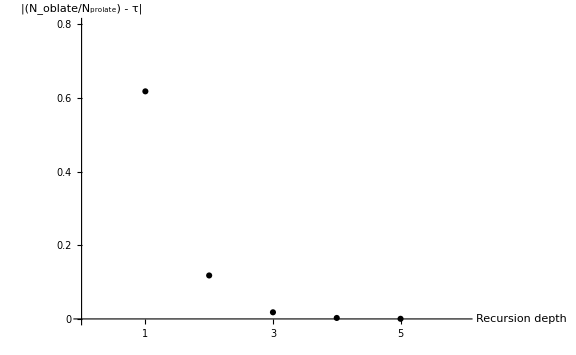
-Graphics-Fig. 4 The convergence of the Penrose tiling to the Golden Ratio

```mathematica
Labeled[ListPlot[Abs[{1,3/2,8/5,21/13,275/170}-GoldenRatio],],]
```